# Linear approximation to a function

```mathematica
f1[x_]:=Cos[x^5-1]/(1+x^3);
f2[x_]:=Cos[x]/(1-Cos[2  x]/(2+Sin[x])^2);
f3[x_]:=Cos[x]/(1-Cos[2  x]/(1+Sin[x])^2);
f4[x_]:=x  Sin[1/x];

(*Choose a point and h for linear approximation*)
x0=2;
h=0.0000001; (*Small h value for approximation*)

(*Define the symmetric difference quotient for derivative approximation*)
DerivativeApproximation[f_,x0_,h_]:=(f[x0+h]-f[x0-h])/(2*h)





(*Compute derivative approximations at x0*)
f1DerivativeApprox=DerivativeApproximation[f1,x0,h];
f2DerivativeApprox=DerivativeApproximation[f2,x0,h];
f3DerivativeApprox=DerivativeApproximation[f3,x0,h];
f4DerivativeApprox=DerivativeApproximation[f4,x0,h];

(*Define the linear approximation functions*)
lf1[x_]:=f1[x0]+f1DerivativeApprox*(x-x0);
lf2[x_]:=f2[x0]+f2DerivativeApprox*(x-x0);
lf3[x_]:=f3[x0]+f3DerivativeApprox*(x-x0);
lf4[x_]:=f4[x0]+f4DerivativeApprox*(x-x0);
```

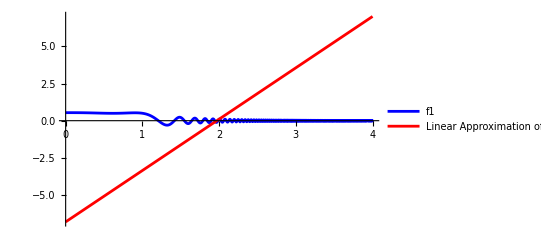

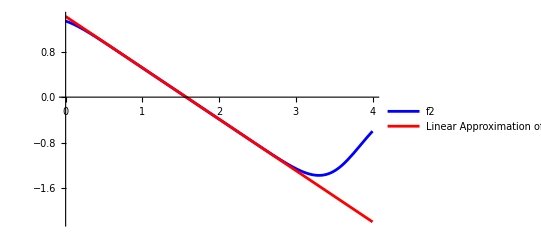

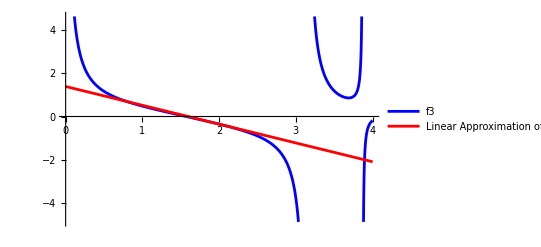

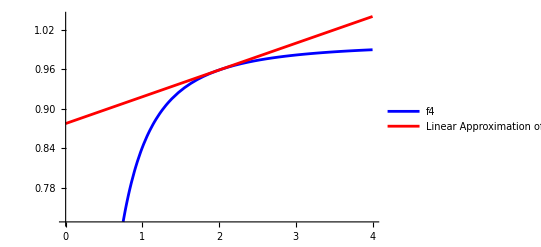

```mathematica
Plot[{f1[x],lf1[x]},{x,x0-2,x0+2},PlotLegends->{"f1","Linear Approximation of f1"},PlotStyle->{Blue,Red}]
Plot[{f2[x],lf2[x]},{x,x0-2,x0+2},PlotLegends->{"f2","Linear Approximation of f2"},PlotStyle->{Blue,Red}]
Plot[{f3[x],lf3[x]},{x,x0-2,x0+2},PlotLegends->{"f3","Linear Approximation of f3"},PlotStyle->{Blue,Red}]
Plot[{f4[x],lf4[x]},{x,x0-2,x0+2},PlotLegends->{"f4","Linear Approximation of f4"},PlotStyle->{Blue,Red}]
```

# Linear approximation to a function Analysis:

For Function 1, f_1(x), the plot displays the function in blue and its linear approximation in red. Near x_0 = 2, the linear approximation is accurate as it closely follows the tangent to the function at this point. However, further from  x_0 , particularly for x < x_0 , the function shows oscillatory behavior due to the x^5 term in the cosine function. This behavior is more complex than what can be represented by a linear trend, leading to a noticeable divergence between the function and its approximation.

For Function 2, f_2(x), if the plot were visible, we would expect to see difficulties in linear approximation near points where the denominator approaches zero, as this would indicate vertical asymptotes or sharp turns in the function. A linear approximation is inadequate near such points due to the rapidly changing behavior of the function, which cannot be captured by a single linear slope.

When linear approximations fail, it may be due to:

- High Curvature: At points of steep curvature, the function’s rate of change is too great for a straight line to provide an accurate approximation.
- Oscillatory Behavior: Rapid oscillations in a function, such as seen with the cos(x^5 - 1) term in  f_1, are not well-captured by a linear approximation.
- Discontinuities or Asymptotes: Linear approximations cannot replicate the behavior of functions at points of discontinuity or vertical asymptotes.

A detailed analysis would involve examining the derivatives at x_0 and the function’s behavior around this point. While the derivative gives the slope of the tangent line and thus the linear approximation, any peculiarities or complex behavior of the function can render this approximation ineffective at capturing the true nature of the function’s behavior.

# The Taylor-Lagrange formula

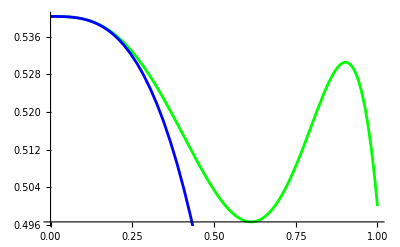

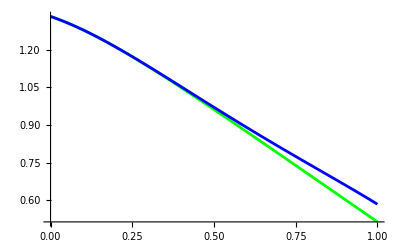

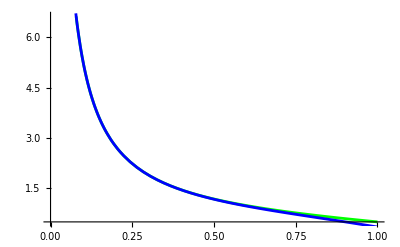

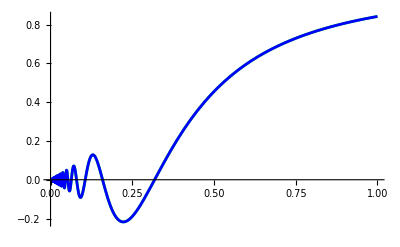

```mathematica
(*Define the functions*)
f1[x_]:=Cos[x^5-1]/(1+x^3)
f2[x_]:=Cos[x]/(1-Cos[2 x]/(2+Sin[x])^2)
f3[x_]:=Cos[x]/(1-Cos[2 x]/(1+Sin[x])^2)
f4[x_]:=x Sin[1/x]

(*Define a function to plot a function,its Taylor polynomial,and the remainder term estimate*)
PlotTaylorLagrangeApproximation[f_,a_,b_,n_]:=Module[{taylorPolynomial,remainderEstimatePlot,taylorPlot,originalFunctionPlot},taylorPolynomial=Normal[Series[f[x],{x,a,n}]];
(*Since we cannot know the exact c,we plot the maximum value of the n-th derivative as an estimate*)remainderEstimatePlot=Plot[Abs[f^(n+1)[x]/(n+1)!]*(b-x)^(n+1),{x,a,b},PlotStyle->Red,PlotRange->All,PlotLabel->"Remainder Term Estimate R_n(x)"];
taylorPlot=Plot[taylorPolynomial,{x,a,b},PlotStyle->Blue];
originalFunctionPlot=Plot[f[x],{x,a,b},PlotStyle->Green];
Show[originalFunctionPlot,taylorPlot,remainderEstimatePlot,PlotLegends->{"f(x)","Taylor Polynomial","Remainder Estimate"}]]

(*Plot for each function*)
PlotTaylorLagrangeApproximation[f1,0,1,4]
PlotTaylorLagrangeApproximation[f2,0,1,4]
PlotTaylorLagrangeApproximation[f3,0,1,4]
PlotTaylorLagrangeApproximation[f4,0,1,4]
```

# Estimating the Derivative at a Point Linear approximation & Improved version

```mathematica
(*Define the function and its derivative*)f[x_]:=Sin[x]
fPrime[x_]:=Cos[x]

(*Define the linear approximation of the derivative*)
linearApprox[f_,x_,h_]:=(f[x+h]-f[x])/h

(*Define the improved approximation of the derivative*)
improvedApprox[f_,x_,h_]:=(f[x+h]-f[x-h])/(2*h)

(*Define the absolute and relative error functions*)
absoluteError[true_,approx_]:=Abs[true-approx]
relativeError[true_,approx_]:=Abs[true-approx]/Abs[true]

(*Choose a point for the derivative approximation*)
x0=1;

(*Create a plot for the linear approximation errors*)
Plot[{absoluteError[fPrime[x0],linearApprox[f,x0,h]],relativeError[fPrime[x0],linearApprox[f,x0,h]]},{h,10^-6,10^-1},PlotRange->All,PlotLabels->{"Absolute Error Linear","Relative Error Linear"},PlotStyle->{Blue,Red},PlotLegends->"Expressions"]

(*Create a plot for the improved approximation errors*)
Plot[{absoluteError[fPrime[x0],improvedApprox[f,x0,h]],relativeError[fPrime[x0],improvedApprox[f,x0,h]]},{h,10^-6,10^-1},PlotRange->All,PlotLabels->{"Absolute Error Improved","Relative Error Improved"},PlotStyle->{Green,Orange},PlotLegends->"Expressions"]
```

-Graphics-

-Graphics-